```mathematica
SymbolToGraph[v24x35]
```

K2

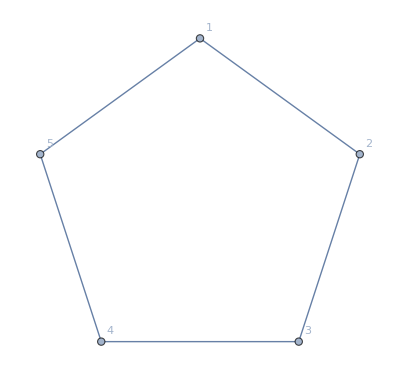
-Graphics-
{{}→v13x24x5+v13x25x4+v13x2x4x5+v14x25x3+v14x2x35+v14x2x3x5+v1x24x35+v1x24x3x5+v1x25x3x4+v1x2x35x4+v1x2x3x4x5,{1}→v24x35 (-2+x)+v24x3x5 (-2+x)+v2x35x4 (-2+x)+v2x3x4x5 (-2+x)+v25x3x4 (-1+x),{2}→v14x35 (-2+x)+v14x3x5 (-2+x)+v1x35x4 (-2+x)+v1x3x4x5 (-2+x)+v13x4x5 (-1+x),{3}→v14x25 (-2+x)+v14x2x5 (-2+x)+v1x25x4 (-2+x)+v1x2x4x5 (-2+x)+v1x24x5 (-1+x),{4}→v13x25 (-2+x)+v13x2x5 (-2+x)+v1x25x3 (-2+x)+v1x2x3x5 (-2+x)+v1x2x35 (-1+x),{5}→v13x24 (-2+x)+v13x2x4 (-2+x)+v1x24x3 (-2+x)+v1x2x3x4 (-2+x)+v14x2x3 (-1+x),{1,2}→v35x4 (-2+x) (-1+x)+v3x4x5 (3-3 x+x^2),{1,3}→v2x4x5 (-2+x)^2+v24x5 (-2+x) (-1+x)+v25x4 (-2+x) (-1+x),{1,4}→v2x3x5 (-2+x)^2+v25x3 (-2+x) (-1+x)+v2x35 (-2+x) (-1+x),{1,5}→v24x3 (-2+x) (-1+x)+v2x3x4 (3-3 x+x^2),{2,3}→v14x5 (-2+x) (-1+x)+v1x4x5 (3-3 x+x^2),{2,4}→v1x3x5 (-2+x)^2+v13x5 (-2+x) (-1+x)+v1x35 (-2+x) (-1+x),{2,5}→v1x3x4 (-2+x)^2+v13x4 (-2+x) (-1+x)+v14x3 (-2+x) (-1+x),{3,4}→v1x25 (-2+x) (-1+x)+v1x2x5 (3-3 x+x^2),{3,5}→v1x2x4 (-2+x)^2+v14x2 (-2+x) (-1+x)+v1x24 (-2+x) (-1+x),{4,5}→v13x2 (-2+x) (-1+x)+v1x2x3 (3-3 x+x^2),{1,2,3}→v4x5 (-2+x) (2-2 x+x^2),{1,2,4}→v35 (-2+x) (-1+x)^2+v3x5 (-2+x) (3-3 x+x^2),{1,2,5}→v3x4 (-2+x) (2-2 x+x^2),{1,3,4}→v25 (-2+x) (-1+x)^2+v2x5 (-2+x) (3-3 x+x^2),{1,3,5}→v24 (-2+x) (-1+x)^2+v2x4 (-2+x) (3-3 x+x^2),{1,4,5}→v2x3 (-2+x) (2-2 x+x^2),{2,3,4}→v1x5 (-2+x) (2-2 x+x^2),{2,3,5}→v14 (-2+x) (-1+x)^2+v1x4 (-2+x) (3-3 x+x^2),{2,4,5}→v13 (-2+x) (-1+x)^2+v1x3 (-2+x) (3-3 x+x^2),{3,4,5}→v1x2 (-2+x) (2-2 x+x^2),{1,2,3,4}→v5 (-2+x) (-1+x) (2-2 x+x^2),{1,2,3,5}→v4 (-2+x) (-1+x) (2-2 x+x^2),{1,2,4,5}→v3 (-2+x) (-1+x) (2-2 x+x^2),{1,3,4,5}→v2 (-2+x) (-1+x) (2-2 x+x^2),{2,3,4,5}→v1 (-2+x) (-1+x) (2-2 x+x^2),{1,2,3,4,5}→(-2+x) (-1+x) x (2-2 x+x^2)}

```mathematica
With[{g=CycleGraph[5]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=MyRewrite4[CalculateInOutFormula[g,s]]},form]
],{s,Subsets[VertexList[g]]}],
s]
}
]
]
```

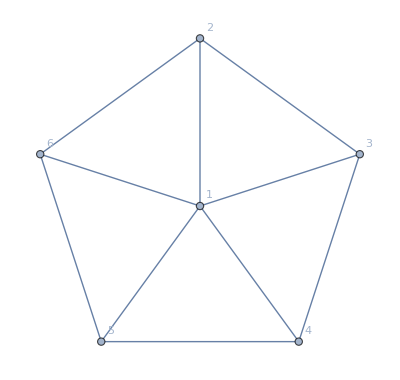
-Graphics-
{{}→v1x24x35x6+v1x24x36x5+v1x24x3x5x6+v1x25x36x4+v1x25x3x46+v1x25x3x4x6+v1x2x35x46+v1x2x35x4x6+v1x2x36x4x5+v1x2x3x46x5+v1x2x3x4x5x6,{1}→v2x3x4x5x6 (-5+x)+v24x3x5x6 (-4+x)+v25x3x4x6 (-4+x)+v2x35x4x6 (-4+x)+v2x36x4x5 (-4+x)+v2x3x46x5 (-4+x)+v24x35x6 (-3+x)+v24x36x5 (-3+x)+v25x36x4 (-3+x)+v25x3x46 (-3+x)+v2x35x46 (-3+x),{2}→v1x35x46 (-3+x)+v1x35x4x6 (-3+x)+v1x3x46x5 (-3+x)+v1x3x4x5x6 (-3+x)+v1x36x4x5 (-2+x),{3}→v1x25x46 (-3+x)+v1x25x4x6 (-3+x)+v1x2x46x5 (-3+x)+v1x2x4x5x6 (-3+x)+v1x24x5x6 (-2+x),{4}→v1x25x36 (-3+x)+v1x25x3x6 (-3+x)+v1x2x36x5 (-3+x)+v1x2x3x5x6 (-3+x)+v1x2x35x6 (-2+x),{5}→v1x24x36 (-3+x)+v1x24x3x6 (-3+x)+v1x2x36x4 (-3+x)+v1x2x3x4x6 (-3+x)+v1x2x3x46 (-2+x),{6}→v1x24x35 (-3+x)+v1x24x3x5 (-3+x)+v1x2x35x4 (-3+x)+v1x2x3x4x5 (-3+x)+v1x25x3x4 (-2+x),{1,2}→v3x4x5x6 (-4+x) (-3+x)+v35x4x6 (-3+x)^2+v3x46x5 (-3+x)^2+v35x46 (-3+x) (-2+x)+v36x4x5 (-3+x) (-2+x),{1,3}→v2x4x5x6 (-4+x) (-3+x)+v25x4x6 (-3+x)^2+v2x46x5 (-3+x)^2+v24x5x6 (-3+x) (-2+x)+v25x46 (-3+x) (-2+x),{1,4}→v2x3x5x6 (-4+x) (-3+x)+v25x3x6 (-3+x)^2+v2x36x5 (-3+x)^2+v25x36 (-3+x) (-2+x)+v2x35x6 (-3+x) (-2+x),{1,5}→v2x3x4x6 (-4+x) (-3+x)+v24x3x6 (-3+x)^2+v2x36x4 (-3+x)^2+v24x36 (-3+x) (-2+x)+v2x3x46 (-3+x) (-2+x),{1,6}→v2x3x4x5 (-4+x) (-3+x)+v24x3x5 (-3+x)^2+v2x35x4 (-3+x)^2+v24x35 (-3+x) (-2+x)+v25x3x4 (-3+x) (-2+x),{2,3}→v1x46x5 (-3+x) (-2+x)+v1x4x5x6 (7-5 x+x^2),{2,4}→v1x3x5x6 (-3+x)^2+v1x35x6 (-3+x) (-2+x)+v1x36x5 (-3+x) (-2+x),{2,5}→v1x3x4x6 (-3+x)^2+v1x36x4 (-3+x) (-2+x)+v1x3x46 (-3+x) (-2+x),{2,6}→v1x35x4 (-3+x) (-2+x)+v1x3x4x5 (7-5 x+x^2),{3,4}→v1x25x6 (-3+x) (-2+x)+v1x2x5x6 (7-5 x+x^2),{3,5}→v1x2x4x6 (-3+x)^2+v1x24x6 (-3+x) (-2+x)+v1x2x46 (-3+x) (-2+x),{3,6}→v1x2x4x5 (-3+x)^2+v1x24x5 (-3+x) (-2+x)+v1x25x4 (-3+x) (-2+x),{4,5}→v1x2x36 (-3+x) (-2+x)+v1x2x3x6 (7-5 x+x^2),{4,6}→v1x2x3x5 (-3+x)^2+v1x25x3 (-3+x) (-2+x)+v1x2x35 (-3+x) (-2+x),{5,6}→v1x24x3 (-3+x) (-2+x)+v1x2x3x4 (7-5 x+x^2),{1,2,3}→v46x5 (-3+x) (-2+x)^2+v4x5x6 (-3+x) (7-5 x+x^2),{1,2,4}→v3x5x6 (-3+x)^3+v35x6 (-3+x) (-2+x)^2+v36x5 (-3+x) (-2+x)^2,{1,2,5}→v3x4x6 (-3+x)^3+v36x4 (-3+x) (-2+x)^2+v3x46 (-3+x) (-2+x)^2,{1,2,6}→v35x4 (-3+x) (-2+x)^2+v3x4x5 (-3+x) (7-5 x+x^2),{1,3,4}→v25x6 (-3+x) (-2+x)^2+v2x5x6 (-3+x) (7-5 x+x^2),{1,3,5}→v2x4x6 (-3+x)^3+v24x6 (-3+x) (-2+x)^2+v2x46 (-3+x) (-2+x)^2,{1,3,6}→v2x4x5 (-3+x)^3+v24x5 (-3+x) (-2+x)^2+v25x4 (-3+x) (-2+x)^2,{1,4,5}→v2x36 (-3+x) (-2+x)^2+v2x3x6 (-3+x) (7-5 x+x^2),{1,4,6}→v2x3x5 (-3+x)^3+v25x3 (-3+x) (-2+x)^2+v2x35 (-3+x) (-2+x)^2,{1,5,6}→v24x3 (-3+x) (-2+x)^2+v2x3x4 (-3+x) (7-5 x+x^2),{2,3,4}→v1x5x6 (-3+x) (5-4 x+x^2),{2,3,5}→v1x46 (-3+x) (-2+x)^2+v1x4x6 (-3+x) (7-5 x+x^2),{2,3,6}→v1x4x5 (-3+x) (5-4 x+x^2),{2,4,5}→v1x36 (-3+x) (-2+x)^2+v1x3x6 (-3+x) (7-5 x+x^2),{2,4,6}→v1x35 (-3+x) (-2+x)^2+v1x3x5 (-3+x) (7-5 x+x^2),{2,5,6}→v1x3x4 (-3+x) (5-4 x+x^2),{3,4,5}→v1x2x6 (-3+x) (5-4 x+x^2),{3,4,6}→v1x25 (-3+x) (-2+x)^2+v1x2x5 (-3+x) (7-5 x+x^2),{3,5,6}→v1x24 (-3+x) (-2+x)^2+v1x2x4 (-3+x) (7-5 x+x^2),{4,5,6}→v1x2x3 (-3+x) (5-4 x+x^2),{1,2,3,4}→v5x6 (-3+x) (-2+x) (5-4 x+x^2),{1,2,3,5}→v46 (-3+x) (-2+x)^2 (-1+x)+v4x6 (-3+x) (-2+x) (7-5 x+x^2),{1,2,3,6}→v4x5 (-3+x) (-2+x) (5-4 x+x^2),{1,2,4,5}→v36 (-3+x) (-2+x)^2 (-1+x)+v3x6 (-3+x) (-2+x) (7-5 x+x^2),{1,2,4,6}→v35 (-3+x) (-2+x)^2 (-1+x)+v3x5 (-3+x) (-2+x) (7-5 x+x^2),{1,2,5,6}→v3x4 (-3+x) (-2+x) (5-4 x+x^2),{1,3,4,5}→v2x6 (-3+x) (-2+x) (5-4 x+x^2),{1,3,4,6}→v25 (-3+x) (-2+x)^2 (-1+x)+v2x5 (-3+x) (-2+x) (7-5 x+x^2),{1,3,5,6}→v24 (-3+x) (-2+x)^2 (-1+x)+v2x4 (-3+x) (-2+x) (7-5 x+x^2),{1,4,5,6}→v2x3 (-3+x) (-2+x) (5-4 x+x^2),{2,3,4,5}→v1x6 (-3+x) (-2+x) (5-4 x+x^2),{2,3,4,6}→v1x5 (-3+x) (-2+x) (5-4 x+x^2),{2,3,5,6}→v1x4 (-3+x) (-2+x) (5-4 x+x^2),{2,4,5,6}→v1x3 (-3+x) (-2+x) (5-4 x+x^2),{3,4,5,6}→v1x2 (-3+x) (-2+x) (5-4 x+x^2),{1,2,3,4,5}→v6 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{1,2,3,4,6}→v5 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{1,2,3,5,6}→v4 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{1,2,4,5,6}→v3 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{1,3,4,5,6}→v2 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{2,3,4,5,6}→v1 (-3+x) (-2+x) (-1+x) (5-4 x+x^2),{1,2,3,4,5,6}→(-3+x) (-2+x) (-1+x) x (5-4 x+x^2)}

```mathematica
With[{g=WheelGraph[6]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=MyRewrite4[CalculateInOutFormula[g,s]]},form]
],{s,Subsets[VertexList[g]]}],
s]
}
]
]
```

```mathematica
EdgeList[WheelGraph[6]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

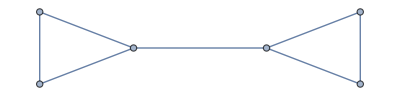

```mathematica
Graph[{1<->2,1<->3,2<->3,1<->4,4<->5,5<->6,6<->4}]
```

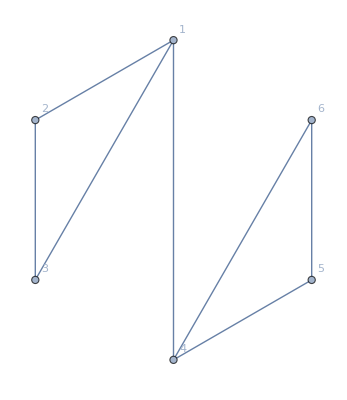
-Graphics-
{{}→v15x24x36+v15x24x3x6+v15x26x34+v15x26x3x4+v15x2x34x6+v15x2x36x4+v15x2x3x4x6+v16x24x35+v16x24x3x5+v16x25x34+v16x25x3x4+v16x2x34x5+v16x2x35x4+v16x2x3x4x5+v1x24x35x6+v1x24x36x5+v1x24x3x5x6+v1x25x34x6+v1x25x36x4+v1x25x3x4x6+v1x26x34x5+v1x26x35x4+v1x26x3x4x5+v1x2x34x5x6+v1x2x35x4x6+v1x2x36x4x5+v1x2x3x4x5x6,{1}→v25x36x4 (-3+x)+v25x3x4x6 (-3+x)+v26x35x4 (-3+x)+v26x3x4x5 (-3+x)+v2x35x4x6 (-3+x)+v2x36x4x5 (-3+x)+v2x3x4x5x6 (-3+x)+v24x35x6 (-2+x)+v24x36x5 (-2+x)+v24x3x5x6 (-2+x)+v25x34x6 (-2+x)+v26x34x5 (-2+x)+v2x34x5x6 (-2+x),{2}→v15x34x6 (-2+x)+v15x36x4 (-2+x)+v15x3x4x6 (-2+x)+v16x34x5 (-2+x)+v16x35x4 (-2+x)+v16x3x4x5 (-2+x)+v1x34x5x6 (-2+x)+v1x35x4x6 (-2+x)+v1x36x4x5 (-2+x)+v1x3x4x5x6 (-2+x),{3}→v15x24x6 (-2+x)+v15x26x4 (-2+x)+v15x2x4x6 (-2+x)+v16x24x5 (-2+x)+v16x25x4 (-2+x)+v16x2x4x5 (-2+x)+v1x24x5x6 (-2+x)+v1x25x4x6 (-2+x)+v1x26x4x5 (-2+x)+v1x2x4x5x6 (-2+x),{4}→v1x25x36 (-3+x)+v1x25x3x6 (-3+x)+v1x26x35 (-3+x)+v1x26x3x5 (-3+x)+v1x2x35x6 (-3+x)+v1x2x36x5 (-3+x)+v1x2x3x5x6 (-3+x)+v15x26x3 (-2+x)+v15x2x36 (-2+x)+v15x2x3x6 (-2+x)+v16x25x3 (-2+x)+v16x2x35 (-2+x)+v16x2x3x5 (-2+x),{5}→v16x24x3 (-2+x)+v16x2x34 (-2+x)+v16x2x3x4 (-2+x)+v1x24x36 (-2+x)+v1x24x3x6 (-2+x)+v1x26x34 (-2+x)+v1x26x3x4 (-2+x)+v1x2x34x6 (-2+x)+v1x2x36x4 (-2+x)+v1x2x3x4x6 (-2+x),{6}→v15x24x3 (-2+x)+v15x2x34 (-2+x)+v15x2x3x4 (-2+x)+v1x24x35 (-2+x)+v1x24x3x5 (-2+x)+v1x25x34 (-2+x)+v1x25x3x4 (-2+x)+v1x2x34x5 (-2+x)+v1x2x35x4 (-2+x)+v1x2x3x4x5 (-2+x),{1,2}→v35x4x6 (-2+x)^2+v36x4x5 (-2+x)^2+v3x4x5x6 (-2+x)^2+v34x5x6 (-2+x) (-1+x),{1,3}→v25x4x6 (-2+x)^2+v26x4x5 (-2+x)^2+v2x4x5x6 (-2+x)^2+v24x5x6 (-2+x) (-1+x),{1,4}→v25x36 (-3+x) (-2+x)+v26x35 (-3+x) (-2+x)+v25x3x6 (7-5 x+x^2)+v26x3x5 (7-5 x+x^2)+v2x35x6 (7-5 x+x^2)+v2x36x5 (7-5 x+x^2)+v2x3x5x6 (8-5 x+x^2),{1,5}→v26x3x4 (-3+x) (-2+x)+v2x36x4 (-3+x) (-2+x)+v2x3x4x6 (-3+x) (-2+x)+v24x36 (-2+x)^2+v24x3x6 (-2+x)^2+v26x34 (-2+x)^2+v2x34x6 (-2+x)^2,{1,6}→v25x3x4 (-3+x) (-2+x)+v2x35x4 (-3+x) (-2+x)+v2x3x4x5 (-3+x) (-2+x)+v24x35 (-2+x)^2+v24x3x5 (-2+x)^2+v25x34 (-2+x)^2+v2x34x5 (-2+x)^2,{2,3}→v15x4x6 (-2+x) (-1+x)+v16x4x5 (-2+x) (-1+x)+v1x4x5x6 (-2+x) (-1+x),{2,4}→v1x35x6 (-3+x) (-2+x)+v1x36x5 (-3+x) (-2+x)+v1x3x5x6 (-3+x) (-2+x)+v15x36 (-2+x)^2+v15x3x6 (-2+x)^2+v16x35 (-2+x)^2+v16x3x5 (-2+x)^2,{2,5}→v16x34 (-2+x)^2+v16x3x4 (-2+x)^2+v1x34x6 (-2+x)^2+v1x36x4 (-2+x)^2+v1x3x4x6 (-2+x)^2,{2,6}→v15x34 (-2+x)^2+v15x3x4 (-2+x)^2+v1x34x5 (-2+x)^2+v1x35x4 (-2+x)^2+v1x3x4x5 (-2+x)^2,{3,4}→v1x25x6 (-3+x) (-2+x)+v1x26x5 (-3+x) (-2+x)+v1x2x5x6 (-3+x) (-2+x)+v15x26 (-2+x)^2+v15x2x6 (-2+x)^2+v16x25 (-2+x)^2+v16x2x5 (-2+x)^2,{3,5}→v16x24 (-2+x)^2+v16x2x4 (-2+x)^2+v1x24x6 (-2+x)^2+v1x26x4 (-2+x)^2+v1x2x4x6 (-2+x)^2,{3,6}→v15x24 (-2+x)^2+v15x2x4 (-2+x)^2+v1x24x5 (-2+x)^2+v1x25x4 (-2+x)^2+v1x2x4x5 (-2+x)^2,{4,5}→v1x26x3 (-2+x)^2+v1x2x36 (-2+x)^2+v1x2x3x6 (-2+x)^2+v16x2x3 (-2+x) (-1+x),{4,6}→v1x25x3 (-2+x)^2+v1x2x35 (-2+x)^2+v1x2x3x5 (-2+x)^2+v15x2x3 (-2+x) (-1+x),{5,6}→v1x24x3 (-2+x) (-1+x)+v1x2x34 (-2+x) (-1+x)+v1x2x3x4 (-2+x) (-1+x),{1,2,3}→v4x5x6 (-2+x) (-1+x)^2,{1,2,4}→v35x6 (-2+x)^3+v36x5 (-2+x)^3+v3x5x6 (-2+x) (5-4 x+x^2),{1,2,5}→v36x4 (-2+x)^3+v3x4x6 (-2+x)^3+v34x6 (-2+x)^2 (-1+x),{1,2,6}→v35x4 (-2+x)^3+v3x4x5 (-2+x)^3+v34x5 (-2+x)^2 (-1+x),{1,3,4}→v25x6 (-2+x)^3+v26x5 (-2+x)^3+v2x5x6 (-2+x) (5-4 x+x^2),{1,3,5}→v26x4 (-2+x)^3+v2x4x6 (-2+x)^3+v24x6 (-2+x)^2 (-1+x),{1,3,6}→v25x4 (-2+x)^3+v2x4x5 (-2+x)^3+v24x5 (-2+x)^2 (-1+x),{1,4,5}→v26x3 (-2+x)^3+v2x36 (-2+x)^3+v2x3x6 (-2+x) (5-4 x+x^2),{1,4,6}→v25x3 (-2+x)^3+v2x35 (-2+x)^3+v2x3x5 (-2+x) (5-4 x+x^2),{1,5,6}→v2x3x4 (-3+x) (-2+x) (-1+x)+v24x3 (-2+x)^2 (-1+x)+v2x34 (-2+x)^2 (-1+x),{2,3,4}→v1x5x6 (-3+x) (-2+x) (-1+x)+v15x6 (-2+x)^2 (-1+x)+v16x5 (-2+x)^2 (-1+x),{2,3,5}→v16x4 (-2+x)^2 (-1+x)+v1x4x6 (-2+x)^2 (-1+x),{2,3,6}→v15x4 (-2+x)^2 (-1+x)+v1x4x5 (-2+x)^2 (-1+x),{2,4,5}→v1x36 (-2+x)^3+v1x3x6 (-2+x)^3+v16x3 (-2+x)^2 (-1+x),{2,4,6}→v1x35 (-2+x)^3+v1x3x5 (-2+x)^3+v15x3 (-2+x)^2 (-1+x),{2,5,6}→v1x34 (-2+x)^2 (-1+x)+v1x3x4 (-2+x)^2 (-1+x),{3,4,5}→v1x26 (-2+x)^3+v1x2x6 (-2+x)^3+v16x2 (-2+x)^2 (-1+x),{3,4,6}→v1x25 (-2+x)^3+v1x2x5 (-2+x)^3+v15x2 (-2+x)^2 (-1+x),{3,5,6}→v1x24 (-2+x)^2 (-1+x)+v1x2x4 (-2+x)^2 (-1+x),{4,5,6}→v1x2x3 (-2+x) (-1+x)^2,{1,2,3,4}→v5x6 (-2+x)^2 (-1+x)^2,{1,2,3,5}→v4x6 (-2+x)^2 (-1+x)^2,{1,2,3,6}→v4x5 (-2+x)^2 (-1+x)^2,{1,2,4,5}→v36 (-2+x)^3 (-1+x)+v3x6 (-2+x)^2 (3-3 x+x^2),{1,2,4,6}→v35 (-2+x)^3 (-1+x)+v3x5 (-2+x)^2 (3-3 x+x^2),{1,2,5,6}→v3x4 (-2+x)^3 (-1+x)+v34 (-2+x)^2 (-1+x)^2,{1,3,4,5}→v26 (-2+x)^3 (-1+x)+v2x6 (-2+x)^2 (3-3 x+x^2),{1,3,4,6}→v25 (-2+x)^3 (-1+x)+v2x5 (-2+x)^2 (3-3 x+x^2),{1,3,5,6}→v2x4 (-2+x)^3 (-1+x)+v24 (-2+x)^2 (-1+x)^2,{1,4,5,6}→v2x3 (-2+x)^2 (-1+x)^2,{2,3,4,5}→v1x6 (-2+x)^3 (-1+x)+v16 (-2+x)^2 (-1+x)^2,{2,3,4,6}→v1x5 (-2+x)^3 (-1+x)+v15 (-2+x)^2 (-1+x)^2,{2,3,5,6}→v1x4 (-2+x)^2 (-1+x)^2,{2,4,5,6}→v1x3 (-2+x)^2 (-1+x)^2,{3,4,5,6}→v1x2 (-2+x)^2 (-1+x)^2,{1,2,3,4,5}→v6 (-2+x)^2 (-1+x)^3,{1,2,3,4,6}→v5 (-2+x)^2 (-1+x)^3,{1,2,3,5,6}→v4 (-2+x)^2 (-1+x)^3,{1,2,4,5,6}→v3 (-2+x)^2 (-1+x)^3,{1,3,4,5,6}→v2 (-2+x)^2 (-1+x)^3,{2,3,4,5,6}→v1 (-2+x)^2 (-1+x)^3,{1,2,3,4,5,6}→(-2+x)^2 (-1+x)^3 x}

```mathematica
With[{g=Graph[{1<->2,1<->3,2<->3,1<->4,4<->5,5<->6,6<->4}]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=MyRewrite4[CalculateInOutFormula[g,s]]},form]
],{s,Subsets[VertexList[g]]}],
s]
}
]
]
```

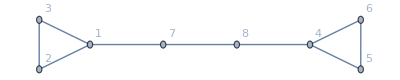

```mathematica
Graph[{1<->2,1<->3,2<->3,1<->7,7<->8,8<->4,4<->5,5<->6,6<->4}, VertexLabels->"Name"]
```

```mathematica
With[{g=Graph[{1<->2,1<->3,2<->3,1<->7,7<->8,8<->4,4<->5,5<->6,6<->4}]},
With[{s={7,8}},
Framed[s->With[{form=MyRewrite4[CalculateInOutFormula[g,s]]},form]
]
]
]
```

{7,8}→v14x25x36 (-2+x) (-1+x)+v14x25x3x6 (-2+x) (-1+x)+v14x26x35 (-2+x) (-1+x)+v14x26x3x5 (-2+x) (-1+x)+v14x2x35x6 (-2+x) (-1+x)+v14x2x36x5 (-2+x) (-1+x)+v14x2x3x5x6 (-2+x) (-1+x)+v15x24x36 (3-3 x+x^2)+v15x24x3x6 (3-3 x+x^2)+v15x26x34 (3-3 x+x^2)+v15x26x3x4 (3-3 x+x^2)+v15x2x34x6 (3-3 x+x^2)+v15x2x36x4 (3-3 x+x^2)+v15x2x3x4x6 (3-3 x+x^2)+v16x24x35 (3-3 x+x^2)+v16x24x3x5 (3-3 x+x^2)+v16x25x34 (3-3 x+x^2)+v16x25x3x4 (3-3 x+x^2)+v16x2x34x5 (3-3 x+x^2)+v16x2x35x4 (3-3 x+x^2)+v16x2x3x4x5 (3-3 x+x^2)+v1x24x35x6 (3-3 x+x^2)+v1x24x36x5 (3-3 x+x^2)+v1x24x3x5x6 (3-3 x+x^2)+v1x25x34x6 (3-3 x+x^2)+v1x25x36x4 (3-3 x+x^2)+v1x25x3x4x6 (3-3 x+x^2)+v1x26x34x5 (3-3 x+x^2)+v1x26x35x4 (3-3 x+x^2)+v1x26x3x4x5 (3-3 x+x^2)+v1x2x34x5x6 (3-3 x+x^2)+v1x2x35x4x6 (3-3 x+x^2)+v1x2x36x4x5 (3-3 x+x^2)+v1x2x3x4x5x6 (3-3 x+x^2)

```mathematica
ToInSymbol[s_]:=SetsToSymbol[SymbolToSets[s],"I"]
```

```mathematica
ToOutSymbol[s_]:=SetsToSymbol[SymbolToSets[s],"O"]
```

```mathematica
CalculateInOutFormulaFull[g_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormulaFull[gContract,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormulaFull[gRemove,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=If[VertexCount[gIn]==0,1,Fold [Plus,Map[ToInSymbol,FindFullFormula[gIn]]]];
resOut=If[VertexCount[gOut]==0,1,Fold [Plus,Map[ToOutSymbol,FindFullFormula[gOut]]]];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

```mathematica
MyRewrite5[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"O"]&]},
If[vars=={},
Factor[form],
Total[
Table[
v*Factor[Last[CoefficientList[form,v]]],
{v,Select[vars,SymbolLevel[#]<=4&]}
]
]
]
]
```

```mathematica
MyRewrite6[form_]:=Block[{vars=Select[DeleteDuplicates[ListofVars[form]],StringStartsQ[ SymbolName[#],"I"]&]},
If[vars=={},
Factor[form],
Total[
Table[
v*Factor[Last[CoefficientList[form,v]]],
{v,Select[vars,SymbolLevel[#]<=4&]}
]
]
]
]
```

```mathematica
With[{g=Graph[{1<->2,1<->3,2<->3,1<->7,7<->8,8<->4,4<->5,5<->6,6<->4}]},
With[{s={7,8,3}},
Framed[s->With[{form=MyRewrite5[CalculateInOutFormulaFull[g,s]]},form]
]
]
]
```

{7,8,3}→(-4+2 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O14x25x6+(-4+2 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O14x26x5+(-4+2 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O14x2x5x6+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O15x24x6+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O15x26x4+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O15x2x4x6+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O16x24x5+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O16x25x4+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O16x2x4x5+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O1x24x5x6+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O1x25x4x6+(-6+3 I3-I37+I37x8-I38+I38x7-I3x7+I3x7x8-I3x8+2 I7-2 I7x8+2 I8) O1x26x4x5

```mathematica
With[{g=WheelGraph[6]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=CalculateInOutFormulaFull[g,s]},MyRewrite5[form]]
],{s,Subsets[VertexList[g]]}],
s]
}
]
]
```

-Graphics-
{{}→{O1x24x35x6+O1x24x36x5+O1x25x36x4+O1x25x3x46+O1x2x35x46,O1x24x35x6+O1x24x36x5+O1x24x3x5x6+O1x25x36x4+O1x25x3x46+O1x25x3x4x6+O1x2x35x46+O1x2x35x4x6+O1x2x36x4x5+O1x2x3x46x5+O1x2x3x4x5x6},{1}→{(-3+I1) O24x35x6+(-3+I1) O24x36x5+(-4+I1) O24x3x5x6+(-3+I1) O25x36x4+(-3+I1) O25x3x46+(-4+I1) O25x3x4x6+(-3+I1) O2x35x46+(-4+I1) O2x35x4x6+(-4+I1) O2x36x4x5+(-4+I1) O2x3x46x5,I1 (O24x35x6+O24x36x5+O24x3x5x6+O25x36x4+O25x3x46+O25x3x4x6+O2x35x46+O2x35x4x6+O2x36x4x5+O2x3x46x5+O2x3x4x5x6)},{2}→{(-3+I2) O1x35x46+(-3+I2) O1x35x4x6+(-2+I2) O1x36x4x5+(-3+I2) O1x3x46x5,I2 (O1x35x46+O1x35x4x6+O1x36x4x5+O1x3x46x5+O1x3x4x5x6)},{3}→{(-2+I3) O1x24x5x6+(-3+I3) O1x25x46+(-3+I3) O1x25x4x6+(-3+I3) O1x2x46x5,I3 (O1x24x5x6+O1x25x46+O1x25x4x6+O1x2x46x5+O1x2x4x5x6)},{4}→{(-3+I4) O1x25x36+(-3+I4) O1x25x3x6+(-2+I4) O1x2x35x6+(-3+I4) O1x2x36x5,I4 (O1x25x36+O1x25x3x6+O1x2x35x6+O1x2x36x5+O1x2x3x5x6)},{5}→{(-3+I5) O1x24x36+(-3+I5) O1x24x3x6+(-3+I5) O1x2x36x4+(-2+I5) O1x2x3x46,I5 (O1x24x36+O1x24x3x6+O1x2x36x4+O1x2x3x46+O1x2x3x4x6)},{6}→{(-3+I6) O1x24x35+(-3+I6) O1x24x3x5+(-2+I6) O1x25x3x4+(-3+I6) O1x2x35x4,I6 (O1x24x35+O1x24x3x5+O1x25x3x4+O1x2x35x4+O1x2x3x4x5)},{1,2}→{(6-2 I1+I1x2-2 I2) O35x46+(9-2 I1+I1x2-3 I2) O35x4x6+(6-I1+I1x2-3 I2) O36x4x5+(9-2 I1+I1x2-3 I2) O3x46x5+(12-2 I1+I1x2-4 I2) O3x4x5x6,I2 (-2 O35x46-3 O35x4x6-3 O36x4x5-3 O3x46x5-4 O3x4x5x6)+I1 (-2 O35x46-2 O35x4x6-O36x4x5-2 O3x46x5-2 O3x4x5x6)+I1x2 (O35x46+O35x4x6+O36x4x5+O3x46x5+O3x4x5x6)},{1,3}→{(6-I1+I1x3-3 I3) O24x5x6+(6-2 I1+I1x3-2 I3) O25x46+(9-2 I1+I1x3-3 I3) O25x4x6+(9-2 I1+I1x3-3 I3) O2x46x5+(12-2 I1+I1x3-4 I3) O2x4x5x6,I3 (-3 O24x5x6-2 O25x46-3 O25x4x6-3 O2x46x5-4 O2x4x5x6)+I1 (-O24x5x6-2 O25x46-2 O25x4x6-2 O2x46x5-2 O2x4x5x6)+I1x3 (O24x5x6+O25x46+O25x4x6+O2x46x5+O2x4x5x6)},{1,4}→{(6-2 I1+I1x4-2 I4) O25x36+(9-2 I1+I1x4-3 I4) O25x3x6+(6-I1+I1x4-3 I4) O2x35x6+(9-2 I1+I1x4-3 I4) O2x36x5+(12-2 I1+I1x4-4 I4) O2x3x5x6,I4 (-2 O25x36-3 O25x3x6-3 O2x35x6-3 O2x36x5-4 O2x3x5x6)+I1 (-2 O25x36-2 O25x3x6-O2x35x6-2 O2x36x5-2 O2x3x5x6)+I1x4 (O25x36+O25x3x6+O2x35x6+O2x36x5+O2x3x5x6)},{1,5}→{(6-2 I1+I1x5-2 I5) O24x36+(9-2 I1+I1x5-3 I5) O24x3x6+(9-2 I1+I1x5-3 I5) O2x36x4+(6-I1+I1x5-3 I5) O2x3x46+(12-2 I1+I1x5-4 I5) O2x3x4x6,I5 (-2 O24x36-3 O24x3x6-3 O2x36x4-3 O2x3x46-4 O2x3x4x6)+I1 (-2 O24x36-2 O24x3x6-2 O2x36x4-O2x3x46-2 O2x3x4x6)+I1x5 (O24x36+O24x3x6+O2x36x4+O2x3x46+O2x3x4x6)},{1,6}→{(6-2 I1+I1x6-2 I6) O24x35+(9-2 I1+I1x6-3 I6) O24x3x5+(6-I1+I1x6-3 I6) O25x3x4+(9-2 I1+I1x6-3 I6) O2x35x4+(12-2 I1+I1x6-4 I6) O2x3x4x5,I6 (-2 O24x35-3 O24x3x5-3 O25x3x4-3 O2x35x4-4 O2x3x4x5)+I1 (-2 O24x35-2 O24x3x5-O25x3x4-2 O2x35x4-2 O2x3x4x5)+I1x6 (O24x35+O24x3x5+O25x3x4+O2x35x4+O2x3x4x5)},{2,3}→{(6-2 I2+I2x3-2 I3) O1x46x5+(7-2 I2+I2x3-2 I3) O1x4x5x6,-2 I2 (O1x46x5+O1x4x5x6)+I2x3 (O1x46x5+O1x4x5x6)-2 I3 (O1x46x5+O1x4x5x6)},{2,4}→{(6-2 I2+I24+I2x4-3 I4) O1x35x6+(6-3 I2+I24+I2x4-2 I4) O1x36x5+(9-3 I2+I24+I2x4-3 I4) O1x3x5x6,I2 (-2 O1x35x6-3 O1x36x5-3 O1x3x5x6)+I4 (-3 O1x35x6-2 O1x36x5-3 O1x3x5x6)+I24 (O1x35x6+O1x36x5+O1x3x5x6)+I2x4 (O1x35x6+O1x36x5+O1x3x5x6)},{2,5}→{(6-3 I2+I25+I2x5-2 I5) O1x36x4+(6-2 I2+I25+I2x5-3 I5) O1x3x46+(9-3 I2+I25+I2x5-3 I5) O1x3x4x6,I5 (-2 O1x36x4-3 O1x3x46-3 O1x3x4x6)+I2 (-3 O1x36x4-2 O1x3x46-3 O1x3x4x6)+I25 (O1x36x4+O1x3x46+O1x3x4x6)+I2x5 (O1x36x4+O1x3x46+O1x3x4x6)},{2,6}→{(6-2 I2+I2x6-2 I6) O1x35x4+(7-2 I2+I2x6-2 I6) O1x3x4x5,-2 I2 (O1x35x4+O1x3x4x5)+I2x6 (O1x35x4+O1x3x4x5)-2 I6 (O1x35x4+O1x3x4x5)},{3,4}→{(6-2 I3+I3x4-2 I4) O1x25x6+(7-2 I3+I3x4-2 I4) O1x2x5x6,-2 I3 (O1x25x6+O1x2x5x6)+I3x4 (O1x25x6+O1x2x5x6)-2 I4 (O1x25x6+O1x2x5x6)},{3,5}→{(6-3 I3+I35+I3x5-2 I5) O1x24x6+(6-2 I3+I35+I3x5-3 I5) O1x2x46+(9-3 I3+I35+I3x5-3 I5) O1x2x4x6,I5 (-2 O1x24x6-3 O1x2x46-3 O1x2x4x6)+I3 (-3 O1x24x6-2 O1x2x46-3 O1x2x4x6)+I35 (O1x24x6+O1x2x46+O1x2x4x6)+I3x5 (O1x24x6+O1x2x46+O1x2x4x6)},{3,6}→{(6-3 I3+I36+I3x6-2 I6) O1x24x5+(6-2 I3+I36+I3x6-3 I6) O1x25x4+(9-3 I3+I36+I3x6-3 I6) O1x2x4x5,I6 (-2 O1x24x5-3 O1x25x4-3 O1x2x4x5)+I3 (-3 O1x24x5-2 O1x25x4-3 O1x2x4x5)+I36 (O1x24x5+O1x25x4+O1x2x4x5)+I3x6 (O1x24x5+O1x25x4+O1x2x4x5)},{4,5}→{(6-2 I4+I4x5-2 I5) O1x2x36+(7-2 I4+I4x5-2 I5) O1x2x3x6,-2 I4 (O1x2x36+O1x2x3x6)+I4x5 (O1x2x36+O1x2x3x6)-2 I5 (O1x2x36+O1x2x3x6)},{4,6}→{(6-2 I4+I46+I4x6-3 I6) O1x25x3+(6-3 I4+I46+I4x6-2 I6) O1x2x35+(9-3 I4+I46+I4x6-3 I6) O1x2x3x5,I4 (-2 O1x25x3-3 O1x2x35-3 O1x2x3x5)+I6 (-3 O1x25x3-2 O1x2x35-3 O1x2x3x5)+I46 (O1x25x3+O1x2x35+O1x2x3x5)+I4x6 (O1x25x3+O1x2x35+O1x2x3x5)},{5,6}→{(6-2 I5+I5x6-2 I6) O1x24x3+(7-2 I5+I5x6-2 I6) O1x2x3x4,-2 I5 (O1x24x3+O1x2x3x4)+I5x6 (O1x24x3+O1x2x3x4)-2 I6 (O1x24x3+O1x2x3x4)},{1,2,3}→{(-12+2 I1-I1x2+I1x2x3-I1x3+4 I2-2 I2x3+4 I3) O46x5+(-21+3 I1-I1x2+I1x2x3-I1x3+6 I2-3 I2x3+6 I3) O4x5x6,I2x3 (-2 O46x5-3 O4x5x6)+I1x2 (-O46x5-O4x5x6)+I1x3 (-O46x5-O4x5x6)+I1x2x3 (O46x5+O4x5x6)+I1 (2 O46x5+3 O4x5x6)+2 I2 (2 O46x5+3 O4x5x6)+2 I3 (2 O46x5+3 O4x5x6)},{1,2,4}→{(-12+2 I1-I1x2+I1x24+I1x2x4-2 I1x4+4 I2-2 I24-2 I2x4+6 I4) O35x6+(-12+2 I1-2 I1x2+I1x24+I1x2x4-I1x4+6 I2-2 I24-2 I2x4+4 I4) O36x5+(-27+4 I1-2 I1x2+I1x24+I1x2x4-2 I1x4+9 I2-3 I24-3 I2x4+9 I4) O3x5x6,I24 (-2 O35x6-2 O36x5-3 O3x5x6)+I2x4 (-2 O35x6-2 O36x5-3 O3x5x6)+I1x2 (-O35x6-2 O36x5-2 O3x5x6)+I1x4 (-2 O35x6-O36x5-2 O3x5x6)+I1x24 (O35x6+O36x5+O3x5x6)+I1x2x4 (O35x6+O36x5+O3x5x6)+2 I1 (O35x6+O36x5+2 O3x5x6)+I4 (6 O35x6+4 O36x5+9 O3x5x6)+I2 (4 O35x6+6 O36x5+9 O3x5x6)},{1,2,5}→{(-12+2 I1-2 I1x2+I1x25+I1x2x5-I1x5+6 I2-2 I25-2 I2x5+4 I5) O36x4+(-12+2 I1-I1x2+I1x25+I1x2x5-2 I1x5+4 I2-2 I25-2 I2x5+6 I5) O3x46+(-27+4 I1-2 I1x2+I1x25+I1x2x5-2 I1x5+9 I2-3 I25-3 I2x5+9 I5) O3x4x6,I25 (-2 O36x4-2 O3x46-3 O3x4x6)+I2x5 (-2 O36x4-2 O3x46-3 O3x4x6)+I1x5 (-O36x4-2 O3x46-2 O3x4x6)+I1x2 (-2 O36x4-O3x46-2 O3x4x6)+I1x25 (O36x4+O3x46+O3x4x6)+I1x2x5 (O36x4+O3x46+O3x4x6)+2 I1 (O36x4+O3x46+2 O3x4x6)+I2 (6 O36x4+4 O3x46+9 O3x4x6)+I5 (4 O36x4+6 O3x46+9 O3x4x6)},{1,2,6}→{(-12+2 I1-I1x2+I1x2x6-I1x6+4 I2-2 I2x6+4 I6) O35x4+(-21+3 I1-I1x2+I1x2x6-I1x6+6 I2-3 I2x6+6 I6) O3x4x5,I2x6 (-2 O35x4-3 O3x4x5)+I1x2 (-O35x4-O3x4x5)+I1x6 (-O35x4-O3x4x5)+I1x2x6 (O35x4+O3x4x5)+I1 (2 O35x4+3 O3x4x5)+2 I2 (2 O35x4+3 O3x4x5)+2 I6 (2 O35x4+3 O3x4x5)},{1,3,4}→{(-12+2 I1-I1x3+I1x3x4-I1x4+4 I3-2 I3x4+4 I4) O25x6+(-21+3 I1-I1x3+I1x3x4-I1x4+6 I3-3 I3x4+6 I4) O2x5x6,I3x4 (-2 O25x6-3 O2x5x6)+I1x3 (-O25x6-O2x5x6)+I1x4 (-O25x6-O2x5x6)+I1x3x4 (O25x6+O2x5x6)+I1 (2 O25x6+3 O2x5x6)+2 I3 (2 O25x6+3 O2x5x6)+2 I4 (2 O25x6+3 O2x5x6)},{1,3,5}→{(-12+2 I1-2 I1x3+I1x35+I1x3x5-I1x5+6 I3-2 I35-2 I3x5+4 I5) O24x6+(-12+2 I1-I1x3+I1x35+I1x3x5-2 I1x5+4 I3-2 I35-2 I3x5+6 I5) O2x46+(-27+4 I1-2 I1x3+I1x35+I1x3x5-2 I1x5+9 I3-3 I35-3 I3x5+9 I5) O2x4x6,I35 (-2 O24x6-2 O2x46-3 O2x4x6)+I3x5 (-2 O24x6-2 O2x46-3 O2x4x6)+I1x5 (-O24x6-2 O2x46-2 O2x4x6)+I1x3 (-2 O24x6-O2x46-2 O2x4x6)+I1x35 (O24x6+O2x46+O2x4x6)+I1x3x5 (O24x6+O2x46+O2x4x6)+2 I1 (O24x6+O2x46+2 O2x4x6)+I3 (6 O24x6+4 O2x46+9 O2x4x6)+I5 (4 O24x6+6 O2x46+9 O2x4x6)},{1,3,6}→{(-12+2 I1-2 I1x3+I1x36+I1x3x6-I1x6+6 I3-2 I36-2 I3x6+4 I6) O24x5+(-12+2 I1-I1x3+I1x36+I1x3x6-2 I1x6+4 I3-2 I36-2 I3x6+6 I6) O25x4+(-27+4 I1-2 I1x3+I1x36+I1x3x6-2 I1x6+9 I3-3 I36-3 I3x6+9 I6) O2x4x5,I36 (-2 O24x5-2 O25x4-3 O2x4x5)+I3x6 (-2 O24x5-2 O25x4-3 O2x4x5)+I1x6 (-O24x5-2 O25x4-2 O2x4x5)+I1x3 (-2 O24x5-O25x4-2 O2x4x5)+I1x36 (O24x5+O25x4+O2x4x5)+I1x3x6 (O24x5+O25x4+O2x4x5)+2 I1 (O24x5+O25x4+2 O2x4x5)+I3 (6 O24x5+4 O25x4+9 O2x4x5)+I6 (4 O24x5+6 O25x4+9 O2x4x5)},{1,4,5}→{(-12+2 I1-I1x4+I1x4x5-I1x5+4 I4-2 I4x5+4 I5) O2x36+(-21+3 I1-I1x4+I1x4x5-I1x5+6 I4-3 I4x5+6 I5) O2x3x6,I4x5 (-2 O2x36-3 O2x3x6)+I1x4 (-O2x36-O2x3x6)+I1x5 (-O2x36-O2x3x6)+I1x4x5 (O2x36+O2x3x6)+I1 (2 O2x36+3 O2x3x6)+2 I4 (2 O2x36+3 O2x3x6)+2 I5 (2 O2x36+3 O2x3x6)},{1,4,6}→{(-12+2 I1-I1x4+I1x46+I1x4x6-2 I1x6+4 I4-2 I46-2 I4x6+6 I6) O25x3+(-12+2 I1-2 I1x4+I1x46+I1x4x6-I1x6+6 I4-2 I46-2 I4x6+4 I6) O2x35+(-27+4 I1-2 I1x4+I1x46+I1x4x6-2 I1x6+9 I4-3 I46-3 I4x6+9 I6) O2x3x5,I46 (-2 O25x3-2 O2x35-3 O2x3x5)+I4x6 (-2 O25x3-2 O2x35-3 O2x3x5)+I1x4 (-O25x3-2 O2x35-2 O2x3x5)+I1x6 (-2 O25x3-O2x35-2 O2x3x5)+I1x46 (O25x3+O2x35+O2x3x5)+I1x4x6 (O25x3+O2x35+O2x3x5)+2 I1 (O25x3+O2x35+2 O2x3x5)+I6 (6 O25x3+4 O2x35+9 O2x3x5)+I4 (4 O25x3+6 O2x35+9 O2x3x5)},{1,5,6}→{(-12+2 I1-I1x5+I1x5x6-I1x6+4 I5-2 I5x6+4 I6) O24x3+(-21+3 I1-I1x5+I1x5x6-I1x6+6 I5-3 I5x6+6 I6) O2x3x4,I5x6 (-2 O24x3-3 O2x3x4)+I1x5 (-O24x3-O2x3x4)+I1x6 (-O24x3-O2x3x4)+I1x5x6 (O24x3+O2x3x4)+I1 (2 O24x3+3 O2x3x4)+2 I5 (2 O24x3+3 O2x3x4)+2 I6 (2 O24x3+3 O2x3x4)},{2,3,4}→{(-15+4 I2-I24+I24x3-2 I2x3+I2x3x4-I2x4+4 I3-2 I3x4+4 I4) O1x5x6,4 I2 O1x5x6-I24 O1x5x6+I24x3 O1x5x6-2 I2x3 O1x5x6+I2x3x4 O1x5x6-I2x4 O1x5x6+4 I3 O1x5x6-2 I3x4 O1x5x6+4 I4 O1x5x6},{2,3,5}→{(-12+4 I2-2 I25+I25x3-2 I2x3+I2x35+I2x3x5-2 I2x5+4 I3-2 I35-2 I3x5+6 I5) O1x46+(-21+6 I2-2 I25+I25x3-3 I2x3+I2x35+I2x3x5-2 I2x5+6 I3-2 I35-2 I3x5+7 I5) O1x4x6,I2x3 (-2 O1x46-3 O1x4x6)-2 I25 (O1x46+O1x4x6)+I25x3 (O1x46+O1x4x6)+I2x35 (O1x46+O1x4x6)+I2x3x5 (O1x46+O1x4x6)-2 I2x5 (O1x46+O1x4x6)-2 I35 (O1x46+O1x4x6)-2 I3x5 (O1x46+O1x4x6)+2 I2 (2 O1x46+3 O1x4x6)+2 I3 (2 O1x46+3 O1x4x6)+I5 (6 O1x46+7 O1x4x6)},{2,3,6}→{(-15+4 I2-2 I2x3+I2x36+I2x3x6-2 I2x6+4 I3-I36-I3x6+4 I6) O1x4x5,4 I2 O1x4x5-2 I2x3 O1x4x5+I2x36 O1x4x5+I2x3x6 O1x4x5-2 I2x6 O1x4x5+4 I3 O1x4x5-I36 O1x4x5-I3x6 O1x4x5+4 I6 O1x4x5},{2,4,5}→{(-12+6 I2-2 I24+I24x5-2 I25+I25x4-2 I2x4+I2x4x5-2 I2x5+4 I4-2 I4x5+4 I5) O1x36+(-21+7 I2-2 I24+I24x5-2 I25+I25x4-2 I2x4+I2x4x5-2 I2x5+6 I4-3 I4x5+6 I5) O1x3x6,I4x5 (-2 O1x36-3 O1x3x6)-2 I24 (O1x36+O1x3x6)+I24x5 (O1x36+O1x3x6)-2 I25 (O1x36+O1x3x6)+I25x4 (O1x36+O1x3x6)-2 I2x4 (O1x36+O1x3x6)+I2x4x5 (O1x36+O1x3x6)-2 I2x5 (O1x36+O1x3x6)+2 I4 (2 O1x36+3 O1x3x6)+2 I5 (2 O1x36+3 O1x3x6)+I2 (6 O1x36+7 O1x3x6)},{2,4,6}→{(-12+4 I2-2 I24+I24x6-2 I2x4+I2x46+I2x4x6-2 I2x6+6 I4-2 I46-2 I4x6+4 I6) O1x35+(-21+6 I2-2 I24+I24x6-2 I2x4+I2x46+I2x4x6-3 I2x6+7 I4-2 I46-2 I4x6+6 I6) O1x3x5,I2x6 (-2 O1x35-3 O1x3x5)-2 I24 (O1x35+O1x3x5)+I24x6 (O1x35+O1x3x5)-2 I2x4 (O1x35+O1x3x5)+I2x46 (O1x35+O1x3x5)+I2x4x6 (O1x35+O1x3x5)-2 I46 (O1x35+O1x3x5)-2 I4x6 (O1x35+O1x3x5)+2 I2 (2 O1x35+3 O1x3x5)+2 I6 (2 O1x35+3 O1x3x5)+I4 (6 O1x35+7 O1x3x5)},{2,5,6}→{(-15+4 I2-I25+I25x6-I2x5+I2x5x6-2 I2x6+4 I5-2 I5x6+4 I6) O1x3x4,4 I2 O1x3x4-I25 O1x3x4+I25x6 O1x3x4-I2x5 O1x3x4+I2x5x6 O1x3x4-2 I2x6 O1x3x4+4 I5 O1x3x4-2 I5x6 O1x3x4+4 I6 O1x3x4},{3,4,5}→{(-15+4 I3-I35+I35x4-2 I3x4+I3x4x5-I3x5+4 I4-2 I4x5+4 I5) O1x2x6,4 I3 O1x2x6-I35 O1x2x6+I35x4 O1x2x6-2 I3x4 O1x2x6+I3x4x5 O1x2x6-I3x5 O1x2x6+4 I4 O1x2x6-2 I4x5 O1x2x6+4 I5 O1x2x6},{3,4,6}→{(-12+4 I3-2 I36+I36x4-2 I3x4+I3x46+I3x4x6-2 I3x6+4 I4-2 I46-2 I4x6+6 I6) O1x25+(-21+6 I3-2 I36+I36x4-3 I3x4+I3x46+I3x4x6-2 I3x6+6 I4-2 I46-2 I4x6+7 I6) O1x2x5,I3x4 (-2 O1x25-3 O1x2x5)-2 I36 (O1x25+O1x2x5)+I36x4 (O1x25+O1x2x5)+I3x46 (O1x25+O1x2x5)+I3x4x6 (O1x25+O1x2x5)-2 I3x6 (O1x25+O1x2x5)-2 I46 (O1x25+O1x2x5)-2 I4x6 (O1x25+O1x2x5)+2 I3 (2 O1x25+3 O1x2x5)+2 I4 (2 O1x25+3 O1x2x5)+I6 (6 O1x25+7 O1x2x5)},{3,5,6}→{(-12+6 I3-2 I35+I35x6-2 I36+I36x5-2 I3x5+I3x5x6-2 I3x6+4 I5-2 I5x6+4 I6) O1x24+(-21+7 I3-2 I35+I35x6-2 I36+I36x5-2 I3x5+I3x5x6-2 I3x6+6 I5-3 I5x6+6 I6) O1x2x4,I5x6 (-2 O1x24-3 O1x2x4)-2 I35 (O1x24+O1x2x4)+I35x6 (O1x24+O1x2x4)-2 I36 (O1x24+O1x2x4)+I36x5 (O1x24+O1x2x4)-2 I3x5 (O1x24+O1x2x4)+I3x5x6 (O1x24+O1x2x4)-2 I3x6 (O1x24+O1x2x4)+2 I5 (2 O1x24+3 O1x2x4)+2 I6 (2 O1x24+3 O1x2x4)+I3 (6 O1x24+7 O1x2x4)},{4,5,6}→{(-15+4 I4-I46+I46x5-2 I4x5+I4x5x6-I4x6+4 I5-2 I5x6+4 I6) O1x2x3,4 I4 O1x2x3-I46 O1x2x3+I46x5 O1x2x3-2 I4x5 O1x2x3+I4x5x6 O1x2x3-I4x6 O1x2x3+4 I5 O1x2x3-2 I5x6 O1x2x3+4 I6 O1x2x3},{1,2,3,4}→{(30-4 I1+I1x2+I1x24x3-I1x2x3+I1x2x3x4+I1x3-I1x3x4+I1x4-8 I2+2 I24-2 I24x3+4 I2x3-2 I2x3x4+2 I2x4-8 I3+4 I3x4-8 I4) O5x6,-4 I1 O5x6+I1x2 O5x6+I1x24x3 O5x6-I1x2x3 O5x6+I1x2x3x4 O5x6+I1x3 O5x6-I1x3x4 O5x6+I1x4 O5x6-8 I2 O5x6+2 I24 O5x6-2 I24x3 O5x6+4 I2x3 O5x6-2 I2x3x4 O5x6+2 I2x4 O5x6-8 I3 O5x6+4 I3x4 O5x6-8 I4 O5x6},{1,2,3,5}→{(12-2 I1+I1x2-I1x25+I1x25x3-I1x2x3+I1x2x35+I1x2x3x5-I1x2x5+I1x3-I1x35-I1x3x5+2 I1x5-4 I2+2 I25-I25x3+2 I2x3-I2x35-I2x3x5+2 I2x5-4 I3+2 I35+2 I3x5-6 I5) O46+(42-6 I1+2 I1x2-I1x25+I1x25x3-2 I1x2x3+I1x2x35+I1x2x3x5-I1x2x5+2 I1x3-I1x35-I1x3x5+3 I1x5-12 I2+4 I25-2 I25x3+6 I2x3-2 I2x35-2 I2x3x5+4 I2x5-12 I3+4 I35+4 I3x5-14 I5) O4x6,I1x2x3 (-O46-2 O4x6)+I25x3 (-O46-2 O4x6)+I2x35 (-O46-2 O4x6)+I2x3x5 (-O46-2 O4x6)+I1x25 (-O46-O4x6)+I1x2x5 (-O46-O4x6)+I1x35 (-O46-O4x6)+I1x3x5 (-O46-O4x6)+I1x25x3 (O46+O4x6)+I1x2x35 (O46+O4x6)+I1x2x3x5 (O46+O4x6)+I1x2 (O46+2 O4x6)+I1x3 (O46+2 O4x6)+2 I25 (O46+2 O4x6)+2 I2x5 (O46+2 O4x6)+2 I35 (O46+2 O4x6)+2 I3x5 (O46+2 O4x6)-2 I1 (O46+3 O4x6)-4 I2 (O46+3 O4x6)+2 I2x3 (O46+3 O4x6)-4 I3 (O46+3 O4x6)+I1x5 (2 O46+3 O4x6)-2 I5 (3 O46+7 O4x6)},{1,2,3,6}→{(30-4 I1+I1x2-I1x2x3+I1x2x36+I1x2x3x6-I1x2x6+I1x3+I1x6-8 I2+4 I2x3-2 I2x36-2 I2x3x6+4 I2x6-8 I3+2 I36+2 I3x6-8 I6) O4x5,-4 I1 O4x5+I1x2 O4x5-I1x2x3 O4x5+I1x2x36 O4x5+I1x2x3x6 O4x5-I1x2x6 O4x5+I1x3 O4x5+I1x6 O4x5-8 I2 O4x5+4 I2x3 O4x5-2 I2x36 O4x5-2 I2x3x6 O4x5+4 I2x6 O4x5-8 I3 O4x5+2 I36 O4x5+2 I3x6 O4x5-8 I6 O4x5},{1,2,4,5}→{(12-2 I1+2 I1x2-I1x24+I1x24x5-I1x25+I1x25x4-I1x2x4+I1x2x4x5-I1x2x5+I1x4-I1x4x5+I1x5-6 I2+2 I24-I24x5+2 I25-I25x4+2 I2x4-I2x4x5+2 I2x5-4 I4+2 I4x5-4 I5) O36+(42-6 I1+3 I1x2-I1x24+I1x24x5-I1x25+I1x25x4-I1x2x4+I1x2x4x5-I1x2x5+2 I1x4-2 I1x4x5+2 I1x5-14 I2+4 I24-2 I24x5+4 I25-2 I25x4+4 I2x4-2 I2x4x5+4 I2x5-12 I4+6 I4x5-12 I5) O3x6,I1x4x5 (-O36-2 O3x6)+I24x5 (-O36-2 O3x6)+I25x4 (-O36-2 O3x6)+I2x4x5 (-O36-2 O3x6)+I1x24 (-O36-O3x6)+I1x25 (-O36-O3x6)+I1x2x4 (-O36-O3x6)+I1x2x5 (-O36-O3x6)+I1x24x5 (O36+O3x6)+I1x25x4 (O36+O3x6)+I1x2x4x5 (O36+O3x6)+I1x4 (O36+2 O3x6)+I1x5 (O36+2 O3x6)+2 I24 (O36+2 O3x6)+2 I25 (O36+2 O3x6)+2 I2x4 (O36+2 O3x6)+2 I2x5 (O36+2 O3x6)-2 I1 (O36+3 O3x6)-4 I4 (O36+3 O3x6)+2 I4x5 (O36+3 O3x6)-4 I5 (O36+3 O3x6)+I1x2 (2 O36+3 O3x6)-2 I2 (3 O36+7 O3x6)},{1,2,4,6}→{(12-2 I1+I1x2-I1x24+I1x24x6-I1x2x4+I1x2x46+I1x2x4x6-I1x2x6+2 I1x4-I1x46-I1x4x6+I1x6-4 I2+2 I24-I24x6+2 I2x4-I2x46-I2x4x6+2 I2x6-6 I4+2 I46+2 I4x6-4 I6) O35+(42-6 I1+2 I1x2-I1x24+I1x24x6-I1x2x4+I1x2x46+I1x2x4x6-2 I1x2x6+3 I1x4-I1x46-I1x4x6+2 I1x6-12 I2+4 I24-2 I24x6+4 I2x4-2 I2x46-2 I2x4x6+6 I2x6-14 I4+4 I46+4 I4x6-12 I6) O3x5,I1x2x6 (-O35-2 O3x5)+I24x6 (-O35-2 O3x5)+I2x46 (-O35-2 O3x5)+I2x4x6 (-O35-2 O3x5)+I1x24 (-O35-O3x5)+I1x2x4 (-O35-O3x5)+I1x46 (-O35-O3x5)+I1x4x6 (-O35-O3x5)+I1x24x6 (O35+O3x5)+I1x2x46 (O35+O3x5)+I1x2x4x6 (O35+O3x5)+I1x2 (O35+2 O3x5)+I1x6 (O35+2 O3x5)+2 I24 (O35+2 O3x5)+2 I2x4 (O35+2 O3x5)+2 I46 (O35+2 O3x5)+2 I4x6 (O35+2 O3x5)-2 I1 (O35+3 O3x5)-4 I2 (O35+3 O3x5)+2 I2x6 (O35+3 O3x5)-4 I6 (O35+3 O3x5)+I1x4 (2 O35+3 O3x5)-2 I4 (3 O35+7 O3x5)},{1,2,5,6}→{(30-4 I1+I1x2+I1x25x6+I1x2x5x6-I1x2x6+I1x5-I1x5x6+I1x6-8 I2+2 I25-2 I25x6+2 I2x5-2 I2x5x6+4 I2x6-8 I5+4 I5x6-8 I6) O3x4,-4 I1 O3x4+I1x2 O3x4+I1x25x6 O3x4+I1x2x5x6 O3x4-I1x2x6 O3x4+I1x5 O3x4-I1x5x6 O3x4+I1x6 O3x4-8 I2 O3x4+2 I25 O3x4-2 I25x6 O3x4+2 I2x5 O3x4-2 I2x5x6 O3x4+4 I2x6 O3x4-8 I5 O3x4+4 I5x6 O3x4-8 I6 O3x4},{1,3,4,5}→{(30-4 I1+I1x3+I1x35x4-I1x3x4+I1x3x4x5+I1x4-I1x4x5+I1x5-8 I3+2 I35-2 I35x4+4 I3x4-2 I3x4x5+2 I3x5-8 I4+4 I4x5-8 I5) O2x6,-4 I1 O2x6+I1x3 O2x6+I1x35x4 O2x6-I1x3x4 O2x6+I1x3x4x5 O2x6+I1x4 O2x6-I1x4x5 O2x6+I1x5 O2x6-8 I3 O2x6+2 I35 O2x6-2 I35x4 O2x6+4 I3x4 O2x6-2 I3x4x5 O2x6+2 I3x5 O2x6-8 I4 O2x6+4 I4x5 O2x6-8 I5 O2x6},{1,3,4,6}→{(12-2 I1+I1x3-I1x36+I1x36x4-I1x3x4+I1x3x46+I1x3x4x6-I1x3x6+I1x4-I1x46-I1x4x6+2 I1x6-4 I3+2 I36-I36x4+2 I3x4-I3x46-I3x4x6+2 I3x6-4 I4+2 I46+2 I4x6-6 I6) O25+(42-6 I1+2 I1x3-I1x36+I1x36x4-2 I1x3x4+I1x3x46+I1x3x4x6-I1x3x6+2 I1x4-I1x46-I1x4x6+3 I1x6-12 I3+4 I36-2 I36x4+6 I3x4-2 I3x46-2 I3x4x6+4 I3x6-12 I4+4 I46+4 I4x6-14 I6) O2x5,I1x3x4 (-O25-2 O2x5)+I36x4 (-O25-2 O2x5)+I3x46 (-O25-2 O2x5)+I3x4x6 (-O25-2 O2x5)+I1x36 (-O25-O2x5)+I1x3x6 (-O25-O2x5)+I1x46 (-O25-O2x5)+I1x4x6 (-O25-O2x5)+I1x36x4 (O25+O2x5)+I1x3x46 (O25+O2x5)+I1x3x4x6 (O25+O2x5)+I1x3 (O25+2 O2x5)+I1x4 (O25+2 O2x5)+2 I36 (O25+2 O2x5)+2 I3x6 (O25+2 O2x5)+2 I46 (O25+2 O2x5)+2 I4x6 (O25+2 O2x5)-2 I1 (O25+3 O2x5)-4 I3 (O25+3 O2x5)+2 I3x4 (O25+3 O2x5)-4 I4 (O25+3 O2x5)+I1x6 (2 O25+3 O2x5)-2 I6 (3 O25+7 O2x5)},{1,3,5,6}→{(12-2 I1+2 I1x3-I1x35+I1x35x6-I1x36+I1x36x5-I1x3x5+I1x3x5x6-I1x3x6+I1x5-I1x5x6+I1x6-6 I3+2 I35-I35x6+2 I36-I36x5+2 I3x5-I3x5x6+2 I3x6-4 I5+2 I5x6-4 I6) O24+(42-6 I1+3 I1x3-I1x35+I1x35x6-I1x36+I1x36x5-I1x3x5+I1x3x5x6-I1x3x6+2 I1x5-2 I1x5x6+2 I1x6-14 I3+4 I35-2 I35x6+4 I36-2 I36x5+4 I3x5-2 I3x5x6+4 I3x6-12 I5+6 I5x6-12 I6) O2x4,I1x5x6 (-O24-2 O2x4)+I35x6 (-O24-2 O2x4)+I36x5 (-O24-2 O2x4)+I3x5x6 (-O24-2 O2x4)+I1x35 (-O24-O2x4)+I1x36 (-O24-O2x4)+I1x3x5 (-O24-O2x4)+I1x3x6 (-O24-O2x4)+I1x35x6 (O24+O2x4)+I1x36x5 (O24+O2x4)+I1x3x5x6 (O24+O2x4)+I1x5 (O24+2 O2x4)+I1x6 (O24+2 O2x4)+2 I35 (O24+2 O2x4)+2 I36 (O24+2 O2x4)+2 I3x5 (O24+2 O2x4)+2 I3x6 (O24+2 O2x4)-2 I1 (O24+3 O2x4)-4 I5 (O24+3 O2x4)+2 I5x6 (O24+3 O2x4)-4 I6 (O24+3 O2x4)+I1x3 (2 O24+3 O2x4)-2 I3 (3 O24+7 O2x4)},{1,4,5,6}→{(30-4 I1+I1x4+I1x46x5-I1x4x5+I1x4x5x6+I1x5-I1x5x6+I1x6-8 I4+2 I46-2 I46x5+4 I4x5-2 I4x5x6+2 I4x6-8 I5+4 I5x6-8 I6) O2x3,-4 I1 O2x3+I1x4 O2x3+I1x46x5 O2x3-I1x4x5 O2x3+I1x4x5x6 O2x3+I1x5 O2x3-I1x5x6 O2x3+I1x6 O2x3-8 I4 O2x3+2 I46 O2x3-2 I46x5 O2x3+4 I4x5 O2x3-2 I4x5x6 O2x3+2 I4x6 O2x3-8 I5 O2x3+4 I5x6 O2x3-8 I6 O2x3},{2,3,4,5}→{(30-8 I2+2 I24-2 I24x3+I24x35+I24x3x5-I24x5+2 I25-I25x3+I25x3x4-I25x4+4 I2x3-I2x35+I2x35x4-2 I2x3x4+I2x3x4x5-I2x3x5+2 I2x4-I2x4x5+2 I2x5-8 I3+2 I35-2 I35x4+4 I3x4-2 I3x4x5+2 I3x5-8 I4+4 I4x5-8 I5) O1x6,-8 I2 O1x6+2 I24 O1x6-2 I24x3 O1x6+I24x35 O1x6+I24x3x5 O1x6-I24x5 O1x6+2 I25 O1x6-I25x3 O1x6+I25x3x4 O1x6-I25x4 O1x6+4 I2x3 O1x6-I2x35 O1x6+I2x35x4 O1x6-2 I2x3x4 O1x6+I2x3x4x5 O1x6-I2x3x5 O1x6+2 I2x4 O1x6-I2x4x5 O1x6+2 I2x5 O1x6-8 I3 O1x6+2 I35 O1x6-2 I35x4 O1x6+4 I3x4 O1x6-2 I3x4x5 O1x6+2 I3x5 O1x6-8 I4 O1x6+4 I4x5 O1x6-8 I5 O1x6},{2,3,4,6}→{(30-8 I2+2 I24-2 I24x3+I24x36+I24x3x6-I24x6+4 I2x3-2 I2x36+I2x36x4-2 I2x3x4+I2x3x46+I2x3x4x6-2 I2x3x6+2 I2x4-I2x46-I2x4x6+4 I2x6-8 I3+2 I36-I36x4+4 I3x4-I3x46-I3x4x6+2 I3x6-8 I4+2 I46+2 I4x6-8 I6) O1x5,-8 I2 O1x5+2 I24 O1x5-2 I24x3 O1x5+I24x36 O1x5+I24x3x6 O1x5-I24x6 O1x5+4 I2x3 O1x5-2 I2x36 O1x5+I2x36x4 O1x5-2 I2x3x4 O1x5+I2x3x46 O1x5+I2x3x4x6 O1x5-2 I2x3x6 O1x5+2 I2x4 O1x5-I2x46 O1x5-I2x4x6 O1x5+4 I2x6 O1x5-8 I3 O1x5+2 I36 O1x5-I36x4 O1x5+4 I3x4 O1x5-I3x46 O1x5-I3x4x6 O1x5+2 I3x6 O1x5-8 I4 O1x5+2 I46 O1x5+2 I4x6 O1x5-8 I6 O1x5},{2,3,5,6}→{(30-8 I2+2 I25-I25x3+I25x36+I25x3x6-2 I25x6+4 I2x3-I2x35+I2x35x6-2 I2x36+I2x36x5-I2x3x5+I2x3x5x6-2 I2x3x6+2 I2x5-2 I2x5x6+4 I2x6-8 I3+2 I35-I35x6+2 I36-I36x5+2 I3x5-I3x5x6+2 I3x6-8 I5+4 I5x6-8 I6) O1x4,-8 I2 O1x4+2 I25 O1x4-I25x3 O1x4+I25x36 O1x4+I25x3x6 O1x4-2 I25x6 O1x4+4 I2x3 O1x4-I2x35 O1x4+I2x35x6 O1x4-2 I2x36 O1x4+I2x36x5 O1x4-I2x3x5 O1x4+I2x3x5x6 O1x4-2 I2x3x6 O1x4+2 I2x5 O1x4-2 I2x5x6 O1x4+4 I2x6 O1x4-8 I3 O1x4+2 I35 O1x4-I35x6 O1x4+2 I36 O1x4-I36x5 O1x4+2 I3x5 O1x4-I3x5x6 O1x4+2 I3x6 O1x4-8 I5 O1x4+4 I5x6 O1x4-8 I6 O1x4},{2,4,5,6}→{(30-8 I2+2 I24-I24x5+I24x5x6-I24x6+2 I25-I25x4+I25x46+I25x4x6-2 I25x6+2 I2x4-I2x46+I2x46x5-I2x4x5+I2x4x5x6-I2x4x6+2 I2x5-2 I2x5x6+4 I2x6-8 I4+2 I46-2 I46x5+4 I4x5-2 I4x5x6+2 I4x6-8 I5+4 I5x6-8 I6) O1x3,-8 I2 O1x3+2 I24 O1x3-I24x5 O1x3+I24x5x6 O1x3-I24x6 O1x3+2 I25 O1x3-I25x4 O1x3+I25x46 O1x3+I25x4x6 O1x3-2 I25x6 O1x3+2 I2x4 O1x3-I2x46 O1x3+I2x46x5 O1x3-I2x4x5 O1x3+I2x4x5x6 O1x3-I2x4x6 O1x3+2 I2x5 O1x3-2 I2x5x6 O1x3+4 I2x6 O1x3-8 I4 O1x3+2 I46 O1x3-2 I46x5 O1x3+4 I4x5 O1x3-2 I4x5x6 O1x3+2 I4x6 O1x3-8 I5 O1x3+4 I5x6 O1x3-8 I6 O1x3},{3,4,5,6}→{(30-8 I3+2 I35-2 I35x4+I35x46+I35x4x6-I35x6+2 I36-I36x4+I36x4x5-I36x5+4 I3x4-I3x46+I3x46x5-2 I3x4x5+I3x4x5x6-I3x4x6+2 I3x5-I3x5x6+2 I3x6-8 I4+2 I46-2 I46x5+4 I4x5-2 I4x5x6+2 I4x6-8 I5+4 I5x6-8 I6) O1x2,-8 I3 O1x2+2 I35 O1x2-2 I35x4 O1x2+I35x46 O1x2+I35x4x6 O1x2-I35x6 O1x2+2 I36 O1x2-I36x4 O1x2+I36x4x5 O1x2-I36x5 O1x2+4 I3x4 O1x2-I3x46 O1x2+I3x46x5 O1x2-2 I3x4x5 O1x2+I3x4x5x6 O1x2-I3x4x6 O1x2+2 I3x5 O1x2-I3x5x6 O1x2+2 I3x6 O1x2-8 I4 O1x2+2 I46 O1x2-2 I46x5 O1x2+4 I4x5 O1x2-2 I4x5x6 O1x2+2 I4x6 O1x2-8 I5 O1x2+4 I5x6 O1x2-8 I6 O1x2},{1,2,3,4,5}→{(-30+4 I1-I1x2-I1x24x3+I1x24x35+I1x24x3x5+I1x25x3x4+I1x2x3+I1x2x35x4-I1x2x3x4+I1x2x3x4x5-I1x3-I1x35x4+I1x3x4-I1x3x4x5-I1x4+I1x4x5-I1x5+8 I2-2 I24+2 I24x3-I24x35-I24x3x5+I24x5-2 I25+I25x3-I25x3x4+I25x4-4 I2x3+I2x35-I2x35x4+2 I2x3x4-I2x3x4x5+I2x3x5-2 I2x4+I2x4x5-2 I2x5+8 I3-2 I35+2 I35x4-4 I3x4+2 I3x4x5-2 I3x5+8 I4-4 I4x5+8 I5) O6,4 I1 O6-I1x2 O6-I1x24x3 O6+I1x24x35 O6+I1x24x3x5 O6+I1x25x3x4 O6+I1x2x3 O6+I1x2x35x4 O6-I1x2x3x4 O6-I1x3 O6-I1x35x4 O6+I1x3x4 O6-I1x3x4x5 O6-I1x4 O6+I1x4x5 O6-I1x5 O6+8 I2 O6-2 I24 O6+2 I24x3 O6-I24x35 O6-I24x3x5 O6+I24x5 O6-2 I25 O6+I25x3 O6-I25x3x4 O6+I25x4 O6-4 I2x3 O6+I2x35 O6-I2x35x4 O6+2 I2x3x4 O6-I2x3x4x5 O6+I2x3x5 O6-2 I2x4 O6+I2x4x5 O6-2 I2x5 O6+8 I3 O6-2 I35 O6+2 I35x4 O6-4 I3x4 O6+2 I3x4x5 O6-2 I3x5 O6+8 I4 O6-4 I4x5 O6+8 I5 O6},{1,2,3,4,6}→{(-30+4 I1-I1x2-I1x24x3+I1x24x36+I1x24x3x6+I1x2x3-I1x2x36+I1x2x36x4-I1x2x3x4+I1x2x3x46+I1x2x3x4x6-I1x2x3x6+I1x2x6-I1x3+I1x3x4-I1x4-I1x6+8 I2-2 I24+2 I24x3-I24x36-I24x3x6+I24x6-4 I2x3+2 I2x36-I2x36x4+2 I2x3x4-I2x3x46-I2x3x4x6+2 I2x3x6-2 I2x4+I2x46+I2x4x6-4 I2x6+8 I3-2 I36+I36x4-4 I3x4+I3x46+I3x4x6-2 I3x6+8 I4-2 I46-2 I4x6+8 I6) O5,4 I1 O5-I1x2 O5-I1x24x3 O5+I1x24x36 O5+I1x24x3x6 O5+I1x2x3 O5-I1x2x36 O5+I1x2x36x4 O5-I1x2x3x4 O5+I1x2x3x46 O5-I1x2x3x6 O5+I1x2x6 O5-I1x3 O5+I1x3x4 O5-I1x4 O5-I1x6 O5+8 I2 O5-2 I24 O5+2 I24x3 O5-I24x36 O5-I24x3x6 O5+I24x6 O5-4 I2x3 O5+2 I2x36 O5-I2x36x4 O5+2 I2x3x4 O5-I2x3x46 O5-I2x3x4x6 O5+2 I2x3x6 O5-2 I2x4 O5+I2x46 O5+I2x4x6 O5-4 I2x6 O5+8 I3 O5-2 I36 O5+I36x4 O5-4 I3x4 O5+I3x46 O5+I3x4x6 O5-2 I3x6 O5+8 I4 O5-2 I46 O5-2 I4x6 O5+8 I6 O5},{1,2,3,5,6}→{(-30+4 I1-I1x2+I1x25x36+I1x25x3x6-I1x25x6+I1x2x3+I1x2x35x6-I1x2x36+I1x2x36x5+I1x2x3x5x6-I1x2x3x6-I1x2x5x6+I1x2x6-I1x3-I1x5+I1x5x6-I1x6+8 I2-2 I25+I25x3-I25x36-I25x3x6+2 I25x6-4 I2x3+I2x35-I2x35x6+2 I2x36-I2x36x5+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+I35x6-2 I36+I36x5-2 I3x5+I3x5x6-2 I3x6+8 I5-4 I5x6+8 I6) O4,4 I1 O4-I1x2 O4+I1x25x36 O4+I1x25x3x6 O4-I1x25x6 O4+I1x2x3 O4+I1x2x35x6 O4-I1x2x36 O4+I1x2x36x5 O4-I1x2x3x6 O4-I1x2x5x6 O4+I1x2x6 O4-I1x3 O4-I1x5 O4+I1x5x6 O4-I1x6 O4+8 I2 O4-2 I25 O4+I25x3 O4-I25x36 O4-I25x3x6 O4+2 I25x6 O4-4 I2x3 O4+I2x35 O4-I2x35x6 O4+2 I2x36 O4-I2x36x5 O4+I2x3x5 O4-I2x3x5x6 O4+2 I2x3x6 O4-2 I2x5 O4+2 I2x5x6 O4-4 I2x6 O4+8 I3 O4-2 I35 O4+I35x6 O4-2 I36 O4+I36x5 O4-2 I3x5 O4+I3x5x6 O4-2 I3x6 O4+8 I5 O4-4 I5x6 O4+8 I6 O4},{1,2,4,5,6}→{(-30+4 I1-I1x2+I1x24x5x6+I1x25x46+I1x25x4x6-I1x25x6+I1x2x46x5+I1x2x4x5x6-I1x2x5x6+I1x2x6-I1x4-I1x46x5+I1x4x5-I1x4x5x6-I1x5+I1x5x6-I1x6+8 I2-2 I24+I24x5-I24x5x6+I24x6-2 I25+I25x4-I25x46-I25x4x6+2 I25x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6) O3,4 I1 O3-I1x2 O3+I1x24x5x6 O3+I1x25x46 O3+I1x25x4x6 O3-I1x25x6 O3+I1x2x46x5 O3-I1x2x5x6 O3+I1x2x6 O3-I1x4 O3-I1x46x5 O3+I1x4x5 O3-I1x4x5x6 O3-I1x5 O3+I1x5x6 O3-I1x6 O3+8 I2 O3-2 I24 O3+I24x5 O3-I24x5x6 O3+I24x6 O3-2 I25 O3+I25x4 O3-I25x46 O3-I25x4x6 O3+2 I25x6 O3-2 I2x4 O3+I2x46 O3-I2x46x5 O3+I2x4x5 O3-I2x4x5x6 O3+I2x4x6 O3-2 I2x5 O3+2 I2x5x6 O3-4 I2x6 O3+8 I4 O3-2 I46 O3+2 I46x5 O3-4 I4x5 O3+2 I4x5x6 O3-2 I4x6 O3+8 I5 O3-4 I5x6 O3+8 I6 O3},{1,3,4,5,6}→{(-30+4 I1-I1x3-I1x35x4+I1x35x46+I1x35x4x6+I1x36x4x5+I1x3x4+I1x3x46x5-I1x3x4x5+I1x3x4x5x6-I1x4-I1x46x5+I1x4x5-I1x4x5x6-I1x5+I1x5x6-I1x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6) O2,4 I1 O2-I1x3 O2-I1x35x4 O2+I1x35x46 O2+I1x35x4x6 O2+I1x36x4x5 O2+I1x3x4 O2+I1x3x46x5 O2-I1x3x4x5 O2-I1x4 O2-I1x46x5 O2+I1x4x5 O2-I1x4x5x6 O2-I1x5 O2+I1x5x6 O2-I1x6 O2+8 I3 O2-2 I35 O2+2 I35x4 O2-I35x46 O2-I35x4x6 O2+I35x6 O2-2 I36 O2+I36x4 O2-I36x4x5 O2+I36x5 O2-4 I3x4 O2+I3x46 O2-I3x46x5 O2+2 I3x4x5 O2-I3x4x5x6 O2+I3x4x6 O2-2 I3x5 O2+I3x5x6 O2-2 I3x6 O2+8 I4 O2-2 I46 O2+2 I46x5 O2-4 I4x5 O2+2 I4x5x6 O2-2 I4x6 O2+8 I5 O2-4 I5x6 O2+8 I6 O2},{2,3,4,5,6}→{(-30+8 I2-2 I24+2 I24x3-I24x35+I24x35x6-I24x36+I24x36x5-I24x3x5+I24x3x5x6-I24x3x6+I24x5-I24x5x6+I24x6-2 I25+I25x3-I25x36+I25x36x4-I25x3x4+I25x3x46+I25x3x4x6-I25x3x6+I25x4-I25x46-I25x4x6+2 I25x6-4 I2x3+I2x35-I2x35x4+I2x35x46+I2x35x4x6-I2x35x6+2 I2x36-I2x36x4+I2x36x4x5-I2x36x5+2 I2x3x4-I2x3x46+I2x3x46x5-I2x3x4x5+I2x3x4x5x6-I2x3x4x6+I2x3x5-I2x3x5x6+2 I2x3x6-2 I2x4+I2x46-I2x46x5+I2x4x5-I2x4x5x6+I2x4x6-2 I2x5+2 I2x5x6-4 I2x6+8 I3-2 I35+2 I35x4-I35x46-I35x4x6+I35x6-2 I36+I36x4-I36x4x5+I36x5-4 I3x4+I3x46-I3x46x5+2 I3x4x5-I3x4x5x6+I3x4x6-2 I3x5+I3x5x6-2 I3x6+8 I4-2 I46+2 I46x5-4 I4x5+2 I4x5x6-2 I4x6+8 I5-4 I5x6+8 I6) O1,8 I2 O1-2 I24 O1+2 I24x3 O1-I24x35 O1+I24x35x6 O1-I24x36 O1+I24x36x5 O1-I24x3x5 O1+I24x3x5x6 O1-I24x3x6 O1+I24x5 O1-I24x5x6 O1+I24x6 O1-2 I25 O1+I25x3 O1-I25x36 O1+I25x36x4 O1-I25x3x4 O1+I25x3x46 O1+I25x3x4x6 O1-I25x3x6 O1+I25x4 O1-I25x46 O1-I25x4x6 O1+2 I25x6 O1-4 I2x3 O1+I2x35 O1-I2x35x4 O1+I2x35x46 O1+I2x35x4x6 O1-I2x35x6 O1+2 I2x36 O1-I2x36x4 O1+I2x36x4x5 O1-I2x36x5 O1+2 I2x3x4 O1-I2x3x46 O1+I2x3x46x5 O1-I2x3x4x5 O1-I2x3x4x6 O1+I2x3x5 O1-I2x3x5x6 O1+2 I2x3x6 O1-2 I2x4 O1+I2x46 O1-I2x46x5 O1+I2x4x5 O1-I2x4x5x6 O1+I2x4x6 O1-2 I2x5 O1+2 I2x5x6 O1-4 I2x6 O1+8 I3 O1-2 I35 O1+2 I35x4 O1-I35x46 O1-I35x4x6 O1+I35x6 O1-2 I36 O1+I36x4 O1-I36x4x5 O1+I36x5 O1-4 I3x4 O1+I3x46 O1-I3x46x5 O1+2 I3x4x5 O1-I3x4x5x6 O1+I3x4x6 O1-2 I3x5 O1+I3x5x6 O1-2 I3x6 O1+8 I4 O1-2 I46 O1+2 I46x5 O1-4 I4x5 O1+2 I4x5x6 O1-2 I4x6 O1+8 I5 O1-4 I5x6 O1+8 I6 O1},{1,2,3,4,5,6}→{I1x24x35x6+I1x24x36x5+I1x24x3x5x6+I1x25x36x4+I1x25x3x46+I1x25x3x4x6+I1x2x35x46+I1x2x35x4x6+I1x2x36x4x5+I1x2x3x46x5+I1x2x3x4x5x6,I1x24x35x6+I1x24x36x5+I1x25x36x4+I1x25x3x46+I1x2x35x46}}

```mathematica
CalculateInOutFormulaValue[g_,in_,out_]:=Block[{
currentEdge, 
edges, 
pos,
isInOut, gContract, gRemove, gIn, gOut, result, resIn, resOut, resContract, resRemove, repVertex},
edges=EdgeList[g];
For[pos=1,pos <=Length[edges],pos++,
currentEdge=edges[[pos]];
isInOut=MemberQ[in,currentEdge[[1]]]&&MemberQ[out,currentEdge[[2]]];
If[!isInOut,
isInOut=MemberQ[in,currentEdge[[2]]]&&MemberQ[out,currentEdge[[1]]];
currentEdge=UndirectedEdge[currentEdge[[2]],currentEdge[[1]]]
];
If[isInOut,
gContract=GContract[g,currentEdge];
repVertex={currentEdge[[1]]->currentEdge[[2]]};
gContract=Graph[VertexList[gContract]/.repVertex,Map[#[[1]]<->#[[2]]/.repVertex&,EdgeList[gContract]]];
gRemove=EdgeDelete[g,currentEdge];
resContract=CalculateInOutFormulaValue[gContract,DeleteCases[in,currentEdge[[1]]],out];
resRemove=CalculateInOutFormulaValue[gRemove,in,out];
(*Print[currentEdge->{Graph[gRemove,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resRemove,Graph[gContract,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resContract}];*)
result=resRemove-resContract;
Return[result]
];
];
gIn=Subgraph[g,in];
gOut=Subgraph[g,out];
resIn=ChromaticPolynomial[gIn,4];
resOut=If[VertexCount[gOut]==0,1,Fold [Plus,FindFullFormula[gOut]]];
(*Print[{Graph[gIn,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"],resIn,Graph[gOut,VertexLabels->"Name", ImageSize->50,GraphLayout->"TutteEmbedding"], resOut,resIn*resOut}];*)
Return[resIn*resOut]
]
```

```mathematica
CalculateInOutFormulaValue[g_,in_]:=CalculateInOutFormulaValue[g,in,Select[VertexList[g],!MemberQ[in,#]&]]
```

```mathematica
CoeffVector
```

```mathematica
Clear[RepCoeff];RepCoeff[base_]:=RepCoeff[base]=Table[allGraphs5[key,Bases[base,"Colofour"]]->BaseCoeff[key,base],{key,Bases[base,"AtomKeys"]}]
```

```mathematica
EdgeList[WheelGraph[6]]
```

{1<->2,1<->3,1<->4,1<->5,1<->6,2<->3,2<->6,3<->4,4<->5,5<->6}

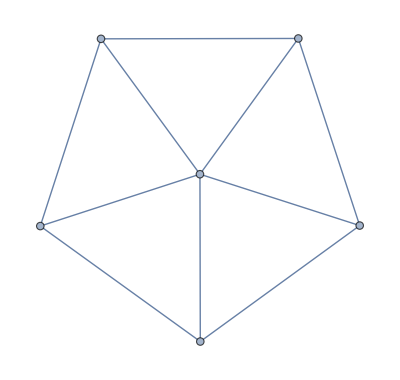

```mathematica
Graph[{6<->2,6<->3,6<->4,6<->5,1<->6,2<->3,2<->1,3<->4,4<->5,5<->1}]
```

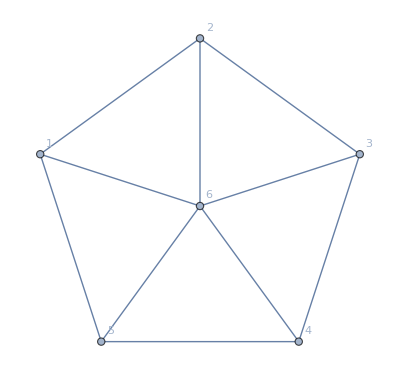
-Graphics-
{{}→v13x24x5x6+v13x25x4x6+v13x2x4x5x6+v14x25x3x6+v14x2x35x6+v14x2x3x5x6+v1x24x35x6+v1x24x3x5x6+v1x25x3x4x6+v1x2x35x4x6+v1x2x3x4x5x6,{6}→v13x24x5+v13x25x4+v14x25x3+v14x2x35+v1x24x35-v1x2x3x4x5,{2}→2 v13x4x5x6+v14x35x6+v14x3x5x6+v1x35x4x6+v1x3x4x5x6,{3}→v14x25x6+v14x2x5x6+2 v1x24x5x6+v1x25x4x6+v1x2x4x5x6,{4}→v13x25x6+v13x2x5x6+v1x25x3x6+2 v1x2x35x6+v1x2x3x5x6,{5}→v13x24x6+v13x2x4x6+2 v14x2x3x6+v1x24x3x6+v1x2x3x4x6,{1}→v24x35x6+v24x3x5x6+2 v25x3x4x6+v2x35x4x6+v2x3x4x5x6,{6,2}→2 v13x4x5+2 v14x35+v14x3x5+v1x35x4,{6,3}→2 v14x25+v14x2x5+2 v1x24x5+v1x25x4,{6,4}→2 v13x25+v13x2x5+v1x25x3+2 v1x2x35}

```mathematica
With[{g=Graph[{6<->2,6<->3,6<->4,6<->5,1<->6,2<->3,2<->1,3<->4,4<->5,5<->1}]},
Column[{Graph[g,GraphLayout->"TutteEmbedding", VertexLabels->"Name"],
Monitor[
Table[
Framed[s->With[{form=Simplify[CalculateInOutFormulaValue[g,s]]},form]
],{s,Take[Subsets[VertexList[g]],10]}],
s]
}
]
]
```